## Common Elements

```mathematica
Needs["HEPMath`"]
DeclareLorentzVectors[l,_p];
```

```mathematica
f1=m@1^2-m@0^2-Sqr[p@1];
f2=m@2^2-m@1^2-Sqr[p@1+p@2]+Sqr[p@1];
f3=m@3^2-m@2^2-Sqr[p@1+p@2+p@3]+Sqr[p@1+p@2];

argsB=argsB01=Sequence[p@1,m@0,m@1];
argsB02=Sequence[p@1+p@2,m@0,m@2];
argsB12=Sequence[p@2,m@1,m@2];
argsC=argsC012=Sequence[p@1,p@2,m@0,m@1,m@2];
argsC013=Sequence[p@1,p@2+p@3,m@0,m@1,m@3];
argsC023=Sequence[p@1+p@2,p@3,m@0,m@2,m@3];
argsC123=Sequence[p@2,p@3,m@1,m@2,m@3];
argsD=Sequence[p@1,p@2,p@3,m@0,m@1,m@2,m@3];
```

```mathematica
repVecs={
Sqr[p@1]-> p12,Sqr[p@2]-> p22,Sqr[p@3]-> p32,
SDot[p@1,p@2]-> sp12,SDot[p@1,p@3]-> sp13,SDot[p@2,p@3]-> sp23,
SDot[p@1+p@2,p@3]-> sp13+sp23,SDot[p@1,p@2+p@3]-> sp12+sp13,
Sqr[p@1+p@2]-> p12+p22+2sp12,Sqr[p@1+p@3]-> p12+p32+2sp13,Sqr[p@2+p@3]-> p22+p32+2sp23,
Sqr[p@1+p@2+p@3]-> p12+p22+p32+2sp12+2sp13+2sp23
};
Module[{l,t},Do[l=HEPExpand[First@e]/.repVecs;t=Simplify[l-Last@e];If[Not[t===0],Print[e, "is not consinstent! ",l]],{e,repVecs}]]
repMasses={m@0^2-> m02,m@1^2-> m12,m@2^2-> m22,m@3^2-> m32};
cmp[a_,b_]:=Simplify[Expand[(a-b)/.repVecs/.repMasses]];
getScalars[x_]:=Module[{l},
l=Reap[x/.{
rA[0][a__]:> Sow[rA[0][a]],
rB[0][a__]:> Sow[rB[0][a]],
rC[0][a__]:> Sow[rC[0][a]],
rD[0][a__]:> Sow[rD[0][a]]
}];
DeleteDuplicates[l[[2,1]]]
];
cmp2[a_,b_]:=Module[{x,y,l,lx,ly,ls},
x=Expand[a/.repVecs/.repMasses];
y=Expand[b/.repVecs/.repMasses];
l=getScalars[x];
lx=CoefficientList[x,l];
ly=CoefficientList[y,l];
ls=Simplify[lx-ly];
Total[ls,Length[l]]
]
```

## Decomposition

### bubble functions B

```mathematica
SetAttributes[rB,Orderless];
rB[1]={q,m0,m1}↦(1/(2Sqr[p@1])(f1 rB[0][argsB]+rA[0][m@0]-rA[0][m@1]))/.{p@1-> q,m@0-> m0,m@1-> m1};
rB[0,0]={q,m0,m1}↦(1/(2(Dim-1))(2m@0^2 rB[0][argsB]+rA[0][m@1]-f1 rB[1][argsB]))/.{p@1-> q,m@0-> m0,m@1-> m1};
rB[1,1]={q,m0,m1}↦(1/(2Sqr[p@1])(f1 rB[1][argsB]+rA[0][m@1]-2rB[0,0][argsB]))/.{p@1-> q,m@0-> m0,m@1-> m1};
```

### triangle functions C

```mathematica
Xc=Table[SDot[p[j],p[k]],{j,2},{k,2}];
iXc=Inverse@Xc;
SetAttributes[rC,Orderless];
```

```mathematica
Module[{S,i},
S={
1/2(f1 rC[0][argsC]+rB[0][argsB02]-rB[0][argsB12]), (* =Subscript[R, 1] *)
1/2(f2 rC[0][argsC]+rB[0][argsB01]-rB[0][argsB02])  (* =Subscript[R, 2] *)
};
i=iXc.S;
rC[1]={q1,q2,m0,m1,m2}↦i[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[2]={q1,q2,m0,m1,m2}↦i[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
]
```

```mathematica
Module[{S00,S11,S12,S21,S22,i1,i2,t},
S00=rB[0][argsB12]+m@0^2 rC[0][argsC];
S11=1/2(f1 rC[1][argsC]+rB[1][argsB02]+rB[0][argsB12]); (* =Subscript[R, 3] *)
S12=1/2(f2 rC[1][argsC]+rB[1][argsB01]-rB[1][argsB02]); (* =Subscript[R, 4] *)
S21=1/2(f1 rC[2][argsC]+rB[1][argsB02]-rB[1][argsB12]); (* =Subscript[R, 5] *)
S22=1/2(f2 rC[2][argsC]-rB[1][argsB02]); (* =Subscript[R, 6] *)

rC[0,0]={q1,q2,m0,m1,m2}↦(1/(Dim-2)(S00-S11-S22))/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
i1=iXc.{S11-rC[0,0][argsC],S12};
rC[1,1]={q1,q2,m0,m1,m2}↦i1[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[1,2]={q1,q2,m0,m1,m2}↦i1[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
i2=iXc.{S21,S22-rC[0,0][argsC]};
rC[2,2]={q1,q2,m0,m1,m2}↦i2[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};

Print["cross check C_21: ",cmp[i2[[1]],rC[2,1][argsC]]];
]
```

cross check C_21: 0

```mathematica
Module[{S,i1,i2,i3,i4,t},
S[0,0,1]=1/2(f1 rC[0,0][argsC]+rB[0,0][argsB02]-rB[0,0][argsB12]); (* =Subscript[R, 10] *)
S[0,0,2]=1/2(f2 rC[0,0][argsC]+rB[0,0][argsB01]-rB[0,0][argsB02]); (* =Subscript[R, 11] *)
i1 = iXc.{S[0,0,1],S[0,0,2]};
rC[0,0,1]={q1,q2,m0,m1,m2}↦i1[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[0,0,2]={q1,q2,m0,m1,m2}↦i1[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};

S[1,1,1]=1/2(f1 rC[1,1][argsC]+rB[1,1][argsB02]-rB[0][argsB12]); (* =Subscript[R, 12] *)
S[1,1,2]=1/2(f2 rC[1,1][argsC]+rB[1,1][argsB01]-rB[1,1][argsB02]); (* =Subscript[R, 13] *)
i2 = iXc.{S[1,1,1]-2rC[0,0,1][argsC],S[1,1,2]};
rC[1,1,1]={q1,q2,m0,m1,m2}↦i2[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[1,1,2]={q1,q2,m0,m1,m2}↦i2[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};

S[2,2,1]=1/2(f1 rC[2,2][argsC]+rB[1,1][argsB02]-rB[1,1][argsB12]); (* =Subscript[R, 14] *)
S[2,2,2]=1/2(f2 rC[2,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 15] *)
i3 = iXc.{S[2,2,1],S[2,2,2]-2rC[0,0,2][argsC]};
rC[2,2,1]={q1,q2,m0,m1,m2}↦i3[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[2,2,2]={q1,q2,m0,m1,m2}↦i3[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
]
```

```mathematica
Module[{S,i4},
S[1,2,1]=1/2(f1 rC[1,2][argsC]+rB[1,1][argsB02]+rB[1][argsB12]); (* =Subscript[R, 16] *)
S[1,2,2]=1/2(f2 rC[1,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 17] *)
i4 = iXc.{S[1,2,1]-rC[0,0,2][argsC],S[1,2,2]-rC[0,0,1][argsC]};
Print["cross check C_121: ",cmp[i4[[1]],rC[1,1,2][argsC]]];
Print["cross check C_122: ",cmp[i4[[2]],rC[1,2,2][argsC]]];
]
```

cross check C_121: 0

cross check C_122: 0

### box function D

```mathematica
Xd=Table[SDot[p[j],p[k]],{j,3},{k,3}];
iXd=Inverse@Xd;
SetAttributes[rD,Orderless];
```

```mathematica
Module[{T,i},
T={
1/2(f1 rD[0][argsD]+rC[0][argsC023]-rC[0][argsC123]), (* =Subscript[R, 20] *)
1/2(f2  rD[0][argsD]+rC[0][argsC013]-rC[0][argsC023]), (* =Subscript[R, 21] *)
1/2(f3  rD[0][argsD]+rC[0][argsC012]-rC[0][argsC013]) (* =Subscript[R, 22] *)
};
i=iXd.T;
rD[1]={q1,q2,q3,m0,m1,m2,m3}↦i[[1]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[2]={q1,q2,q3,m0,m1,m2,m3}↦i[[2]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[3]={q1,q2,q3,m0,m1,m2,m3}↦i[[3]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
]
```

```mathematica
Module[{T,i1,i2,i3},
T[0,0]=m@0^2 rD[0][argsD]+rC[0][argsC123];

T[1,1]=1/2(f1 rD[1][argsD]+rC[1][argsC023]+rC[0][argsC123]);(* =Subscript[R, 30] *)
T[1,2]=1/2(f2 rD[1][argsD]+rC[1][argsC013]-rC[1][argsC023]);(* =Subscript[R, 31] *)
T[1,3]=1/2(f3 rD[1][argsD]+rC[1][argsC012]-rC[1][argsC013]);(* =Subscript[R, 32] *)

T[2,1]=1/2(f1 rD[2][argsD]+rC[1][argsC023]-rC[1][argsC123]);(* =Subscript[R, 33] *)
T[2,2]=1/2(f2 rD[2][argsD]+rC[2][argsC013]-rC[1][argsC023]); (* =Subscript[R, 34] *)
T[2,3]=1/2(f3 rD[2][argsD]+rC[2][argsC012]-rC[2][argsC013]); (* =Subscript[R, 35] *)

T[3,1]=1/2(f1 rD[3][argsD]+rC[2][argsC023]-rC[2][argsC123]); (* =Subscript[R, 36] *)
T[3,2]=1/2(f2 rD[3][argsD]+rC[2][argsC013]-rC[2][argsC023]); (* =Subscript[R, 37] *)
T[3,3]=1/2(f3 rD[3][argsD]-rC[2][argsC013]); (* =Subscript[R, 38] *)

rD[0,0]={q1,q2,q3,m0,m1,m2,m3}↦(1/(Dim-3)(T[0,0]-T[1,1]-T[2,2]-T[3,3]))/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

i1=iXd.{T[1,1]-rD[0,0][argsD],T[1,2],T[1,3]};
rD[1,1]={q1,q2,q3,m0,m1,m2,m3}↦(i1[[1]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[1,2]={q1,q2,q3,m0,m1,m2,m3}↦(i1[[2]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[1,3]={q1,q2,q3,m0,m1,m2,m3}↦(i1[[3]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

i2=iXd.{T[2,1],T[2,2]-rD[0,0][argsD],T[2,3]};
rD[2,2]={q1,q2,q3,m0,m1,m2,m3}↦(i2[[2]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[2,3]={q1,q2,q3,m0,m1,m2,m3}↦(i2[[3]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

i3=iXd.{T[3,1],T[3,2],T[3,3]-rD[0,0][argsD]};
rD[3,3]={q1,q2,q3,m0,m1,m2,m3}↦(i3[[3]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

Print["cross check D_21: ",cmp[i2[[1]],rD[2,1][argsD]]];
Print["cross check D_31: ",cmp[i3[[1]],rD[3,1][argsD]]];
Print["cross check D_32: ",cmp[i3[[2]],rD[3,2][argsD]]];
]
```

cross check D_21: 0

cross check D_31: 0

cross check D_32: 0

```mathematica
Module[{T,i12},
T[0,0,1]=1/2(f1 rD[0,0][argsD]+rC[0,0][argsC023]-rC[0,0][argsC123]); (* =Subscript[R, 40] *)
T[0,0,2]=1/2(f2 rD[0,0][argsD]+rC[0,0][argsC013]-rC[0,0][argsC023]); (* =Subscript[R, 41] *)
T[0,0,3]=1/2(f3 rD[0,0][argsD]+rC[0,0][argsC012]-rC[0,0][argsC013]); (* =Subscript[R, 42] *)

T[1,1,1]=1/2(f1 rD[1,1][argsD]+rC[1,1][argsC023]-rC[0][argsC123]); (* =Subscript[R, 43] *)
T[1,1,2]=1/2(f2 rD[1,1][argsD]+rC[1,1][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 44] *)
T[1,1,3]=1/2(f3 rD[1,1][argsD]+rC[1,1][argsC012]-rC[1,1][argsC013]); (* =Subscript[R, 45] *)

T[2,2,1]=1/2(f1 rD[2,2][argsD]+rC[1,1][argsC023]-rC[1,1][argsC123]); (* =Subscript[R, 46] *)
T[2,2,2]=1/2(f2 rD[2,2][argsD]+rC[2,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 47] *)
T[2,2,3]=1/2(f3 rD[2,2][argsD]+rC[2,2][argsC012]-rC[2,2][argsC013]); (* =Subscript[R, 48] *)

T[3,3,1]=1/2(f1 rD[3,3][argsD]+rC[2,2][argsC023]-rC[2,2][argsC123]); (* =Subscript[R, 49] *)
T[3,3,2]=1/2(f2 rD[3,3][argsD]+rC[2,2][argsC013]-rC[2,2][argsC023]); (* =Subscript[R, 50] *)
T[3,3,3]=1/2(f3 rD[3,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 51] *)

T[1,2,1]=1/2(f1 rD[1,2][argsD]+rC[1,1][argsC023]+rC[1][argsC123]); (* =Subscript[R, 52] *)
T[1,2,2]=1/2(f2 rD[1,2][argsD]+rC[1,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 53] *)
T[1,2,3]=1/2(f3 rD[1,2][argsD]+rC[1,2][argsC012]-rC[1,2][argsC013]); (* =Subscript[R, 54] *)

Do[Module[{v,i},
v={T[n,n,1],T[n,n,2],T[n,n,3]};
If[n>0,v[[n]]-=2rD[0,0,n][argsD]];
i = iXd.v;
rD[n,n,1]={q1,q2,q3,m0,m1,m2,m3}↦i[[1]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[n,n,2]={q1,q2,q3,m0,m1,m2,m3}↦i[[2]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[n,n,3]={q1,q2,q3,m0,m1,m2,m3}↦i[[3]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
],{n,0,3}];

i12= iXd.{T[1,2,1]-rD[0,0,2][argsD],T[1,2,2]-rD[0,0,1][argsD],T[1,2,3]};
rD[1,2,3]={q1,q2,q3,m0,m1,m2,m3}↦i12[[3]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

Print["cross check D_121: ",cmp2[i12[[1]],rD[1,2,1][argsD]]];
Print["cross check D_122: ",cmp2[i12[[2]],rD[1,2,2][argsD]]];
]
```

cross check D_121: 0

cross check D_122: 0

```mathematica
Module[{T,i13,i23,a,b},
T[1,3,1]=1/2(f1 rD[1,3][argsD]+rC[1,2][argsC023]+rC[2][argsC123]); (* =Subscript[R, 55] *)
T[1,3,2]=1/2(f2 rD[1,3][argsD]+rC[1,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 56] *)
T[1,3,3]=1/2(f3 rD[1,3][argsD]-rC[1,2][argsC013]); (* =Subscript[R, 57] *)

T[2,3,1]=1/2(f1 rD[2,3][argsD]+rC[1,2][argsC023]-rC[1,2][argsC123]); (* =Subscript[R, 58] *)
T[2,3,2]=1/2(f2 rD[2,3][argsD]+rC[2,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 59] *)
T[2,3,3]=1/2(f3 rD[2,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 60] *)

i13= iXd.{T[1,3,1]-rD[0,0,3][argsD],T[1,3,2],T[1,3,3]-rD[0,0,1][argsD]};
i23= iXd.{T[2,3,1],T[2,3,2]-rD[0,0,3][argsD],T[2,3,3]-rD[0,0,2][argsD]};

a=i13[[1]];
b=rD[1,3,1][argsD];

Print["cross check D_131: ",cmp2[i13[[1]],rD[1,3,1][argsD]]];
Print["cross check D_132: ",cmp2[i13[[2]],rD[1,3,2][argsD]]];
Print["cross check D_133: ",cmp2[i13[[3]],rD[1,3,3][argsD]]];
Print["cross check D_231: ",cmp2[i23[[1]],rD[2,3,1][argsD]]];
Print["cross check D_232: ",cmp2[i23[[2]],rD[2,3,2][argsD]]];
Print["cross check D_233: ",cmp2[i23[[3]],rD[2,3,3][argsD]]];
]
```

cross check D_131: 0

cross check D_132: 0

cross check D_133: 0

cross check D_231: 0

cross check D_232: 0

cross check D_233: 0

### Check to Marco

```mathematica
Module[{r,map,a,b,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_C.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],n-> Dim};
map={
c11-> 1,
c12-> 2,
c24->{0,0},
c21-> {1,1},
c22-> {2,2},
c23-> {1,2},
c31-> {1,1,1},
c32-> {2,2,2},
c33-> {1,1,2},
c34-> {1,2,2},
c35-> {0,0,1},
c36-> {0,0,2}
};
Do[
a=((First@e)[argsC]/.r);
b=rC[(Last@e)/.{List-> Sequence}][argsC];
Print@cmp[a,b];
,{e,map}]
]
```

0

0

0

«9 more identical outputs»

```mathematica
Module[{r,map,a,b,ca,cb,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_D.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],d0-> rD[0],n-> Dim};
map={
d11-> 1,
d12-> 2,
d13-> 3,
d21-> {1,1},
d22-> {2,2},
d23-> {3,3},
d24-> {1,2},
d25-> {1,3},
d26-> {2,3},
d27-> {0,0},
d31-> {1,1,1},
d32-> {2,2,2},
d33-> {3,3,3},
d34-> {1,1,2},
d35-> {1,1,3},
d36-> {1,2,2},
d37->{1,3,3},
d38-> {2,2,3},
d39->{2,3,3},
d310-> {1,2,3},
d311-> {0,0,1},
d312-> {0,0,2},
d313-> {0,0,3}
};
Do[
a=((First@e)[argsD]/.r);
b=rD[(Last@e)/.{List-> Sequence}][argsD];
Print@cmp[a,b];
,{e,map}]
]
```

0

0

0

«20 more identical outputs»

## Scalar Integrals

```mathematica
getScalars[rC[1][-p1-p2,q,m2,m2,m2]]
getScalars[rC[2][-p1-p2,q,m2,m2,m2]]
```

{rB[0][q,m2,m2],rB[0][-p1-p2+q,m2,m2],rC[0][-p1-p2,q,m2,m2,m2],rB[0][-p1-p2,m2,m2]}

{rB[0][q,m2,m2],rB[0][-p1-p2+q,m2,m2],rC[0][-p1-p2,q,m2,m2,m2],rB[0][-p1-p2,m2,m2]}

```mathematica
rC[1][-p1-p2,q,m2,m2,m2]
```

(Sqr[q] (-rB[0][q,m2,m2]+rB[0][-p1-p2+q,m2,m2]-Sqr[-p1-p2] rC[0][-p1-p2,q,m2,m2,m2]))/(2 (-SDot[-p1-p2,q]^2+Sqr[-p1-p2] Sqr[q]))-(SDot[-p1-p2,q] (rB[0][-p1-p2,m2,m2]-rB[0][-p1-p2+q,m2,m2]+(Sqr[-p1-p2]-Sqr[-p1-p2+q]) rC[0][-p1-p2,q,m2,m2,m2]))/(2 (-SDot[-p1-p2,q]^2+Sqr[-p1-p2] Sqr[q]))

### A_0

```mathematica
fBeen2Den=(2π)^4/(I π^2)
Cϵ=1/(16π^2)Exp[ϵ/2(EulerGamma-Log[4π])](m2/μ2)^(ϵ/2);
Module[{A0Den,A0Been},
A0Den[m2_]=-m2(m2/(4π μ2))^(ϵ/2)Gamma[-1-ϵ/2];
Print@Simplify@Series[A0Den[m2],{ϵ,0,0}];
A0Been[m2_]=I Cϵ m2(-2/ϵ+1);
Print@Simplify@Series[A0Been[m2],{ϵ,0,0}];
Print@FullSimplify[Series[A0Den[m2],{ϵ,0,2}]-Series[fBeen2Den*A0Been[m2],{ϵ,0,2}]];
]
```

-16 ⅈ π^2

-(2 m2)/ϵ-m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2])+O[ϵ]^1

-(ⅈ m2)/(8 π^2 ϵ)-(ⅈ m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2]))/(16 π^2)+O[ϵ]^1

-1/24 (m2 (12+π^2)) ϵ+1/48 m2 (-EulerGamma (12+π^2)+π^2 (1+Log[4]+Log[π])-(12+π^2) Log[m2/μ2]+4 (3+Log[64]+3 Log[π]-Zeta[3])) ϵ^2+O[ϵ]^3

### B_0

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((2m2-p2)/m2) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m2/μ2]-m2/p2(1/r-r)Log@r;
Print@FullSimplify[B0/.rSol//.{p2-> s,s-> 4m2/ρ,ρ-> 1-β^2},Assumptions-> {0<β<1,m2>0}];
]
```

{{r→-(-2 m2+p2-√(-4 m2 p2+p2^2))/(2 m2)},{r→-(-2 m2+p2+√(-4 m2 p2+p2^2))/(2 m2)}}

{2-EulerGamma-2/ϵ+Log[4]+Log[π]+β Log[(-1+β)/(1+β)]-Log[m2/μ2],2-EulerGamma-2/ϵ+Log[4]+Log[π]-β Log[(1+β)/(-1+β)]-Log[m2/μ2]}

```mathematica
sB0[p2_,m2_,m2_]=Normal@Series[ I Cϵ(-2/ϵ+2+b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-4m2/p2]},{ϵ,0,0}]
sB0[0,m2_,m2_]=Normal@Series[ I Cϵ(-2/ϵ),{ϵ,0,0}]
```

-ⅈ/(8 π^2 ϵ)-(ⅈ (-2+EulerGamma-√((-4 m2+p2)/p2) Log[(1-√(1-(4 m2)/p2))/(1+√(1-(4 m2)/p2))]-Log[4 π]+Log[m2/μ2]))/(16 π^2)

-ⅈ/(8 π^2 ϵ)-(ⅈ (EulerGamma-Log[4 π]+Log[m2/μ2]))/(16 π^2)

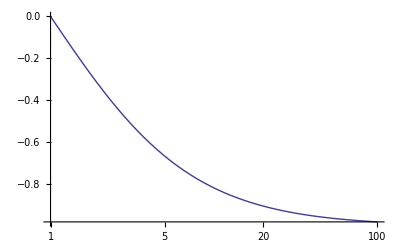

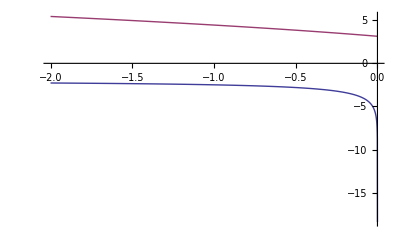

```mathematica
LogLinearPlot[(1-b)/(1+b),{b,1,100}]
Plot[{Re@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]},Im@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]}},{r,-2,0}]
```

### C_0

```mathematica
κ[x_,y_,z_]:=Sqrt[x^2+y^2+z^2-2(x y +y z + z x)];
Series[κ[x2,m2,m2],{x2,0,1}]
```

2 √-m2 √x2+O[x2]^(3/2)

```mathematica
Limit[-PolyLog[2,2/(1-b)]-PolyLog[2,2/(1+b)],b-> ∞,Assumptions-> {M2>0}]
Limit[-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))],q2-> 0,Assumptions-> {M2>0}]
```

0

0

```mathematica
Zeta[2]
```

π^2/6

```mathematica
Module[{sol},
sol=Solve[x==(1-b)/(1+b),b];
Print@sol;
Print@Simplify[{1-x,1-1/x}/.{x-> (1-b)/(1+b)}];
]
```

{{b→(1-x)/(1+x)}}

{(2 b)/(1+b),(2 b)/(-1+b)}

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C},
p2[1]=p2[1,0]=s;
p2[2]=p2[2,0]=k2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
Print@Limit[αα,k2-> 0,Assumptions-> {s>0,s-q2>0}];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print[{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print@α[i];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print[{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print@Limit[y[0,i],k2->0,Assumptions-> {s>0,s-q2>0,M2>0}];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> {s>4M2>0,q2<0,s-q2>0}];
Print@C;
Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];
]
```

-q2+s

{0,1,2}

√(q2 (-4 M2+q2))

{(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

0

{1,2,0}

√(k2 (k2-4 M2))

{(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

q2/(q2-s)

{2,0,1}

√(s (-4 M2+s))

{(s+√(s (-4 M2+s)))/(2 s),(s-√(s (-4 M2+s)))/(2 s)}

1

(-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))])/(√(k2^2+q2^2+s^2-2 (k2 q2+k2 s+q2 s)))

1/(q2-s)(-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))]+PolyLog[2,(2 s)/(s-√(s (-4 M2+s)))]+PolyLog[2,(2 s)/(s+√(s (-4 M2+s)))])

-((-1+β^2) (-1+βq^2) (PolyLog[2,-2/(-1+β)]+PolyLog[2,2/(1+β)]-PolyLog[2,-2/(-1+βq)]-PolyLog[2,2/(1+βq)]))/(4 M2 (β^2-βq^2))

```mathematica
Simplify[(2 q2)/(q2+√(q2 (-4 M2+q2)))/.{q2-> 4M2/ρq},Assumptions-> {M2>0,ρq<0}]
Simplify[(2 q2)/(q2-√(q2 (-4 M2+q2)))/.{q2-> 4M2/ρq},Assumptions-> {M2>0,ρq<0}]
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],3Zeta@2+Log[x]^2/2-Log[x]Log[-x]}/.{x-> (1-b)/(1+b)}/.{b-> {.1,.3,1.1,1.3}}
Limit[-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))],q2-> 0]
```

-2/(-1+√(1-ρq))

2/(1+√(1-ρq))

{{4.91467-4.38675 ⅈ,4.7432-4.65146 ⅈ,-4.63456,-2.07444},{4.91467+0.630426 ⅈ,4.7432+1.94477 ⅈ,-4.63456+0. ⅈ,-2.07444+0. ⅈ}}

0

```mathematica
Module[{K,iy,kx,iyx,r},
K=(1-β^2-4(1-x)x y)/(1-β^2);
Print@K;
iy=Integrate[1/K,y];
kx=FullSimplify[Limit[iy,y-> 1]-Limit[iy,y->0],Assumptions->{0<β<1}];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x];
r=FullSimplify[Limit[iyx,x->1]-Limit[iyx,x->0],Assumptions->{0<β<1}];
Print@Simplify[r*4m2/(s(1-β^2))];
]
```

(1-4 (1-x) x y-β^2)/(1-β^2)

((-1+β^2) (Log[-1+β^2]-Log[-1-4 (-1+x) x+β^2]))/(4 (-1+x) x)

-(m2 (-4 ArcTanh[β]^2+π (π-12 ⅈ Log[2]+2 ⅈ Log[1-β^2])))/(2 s)

```mathematica
FullSimplify[(1-x)/(1-(1/x))]
```

-x

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={0<ρ<1,ρq<0};
K=Simplify[(-a b *0-a c *s-b c q2+a m2+b m2+c m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq}];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(ρ ρq+4 x ((-1+y) ρ-y ρq)+4 x^2 (ρ-y ρ+y ρq))/(ρ ρq)

(ρ ρq (Log[ρ]-Log[(4 (-1+x) x+ρ) ρq]+Log[4 (-1+x) x+ρq]))/(4 (-1+x) x (ρ-ρq))

-1/(4 (ρ-ρq))ρ ρq (-Log[-1/2+x-(√(1-ρ))/2] Log[(2 (-1+x))/(-1+√(1-ρ))]-Log[x+1/2 (-1+√(1-ρ))] Log[(2-2 x)/(1+√(1-ρ))]+Log[1-x] Log[ρ]+Log[-1/2+x-(√(1-ρq))/2] Log[(2 (-1+x))/(-1+√(1-ρq))]+Log[x+1/2 (-1+√(1-ρq))] Log[(2-2 x)/(1+√(1-ρq))]+Log[-1+x] (Log[x+1/2 (-1+√(1-ρ))]+Log[-1/2+x-(√(1-ρ))/2]-Log[(-4 x+4 x^2+ρ) ρq])-Log[-1+x] (Log[x+1/2 (-1+√(1-ρq))]+Log[-1/2+x-(√(1-ρq))/2]-Log[-4 x+4 x^2+ρq])-PolyLog[2,(1-2 x+√(1-ρ))/(-1+√(1-ρ))]-PolyLog[2,(-1+2 x+√(1-ρ))/(1+√(1-ρ))]+PolyLog[2,(1-2 x+√(1-ρq))/(-1+√(1-ρq))]+PolyLog[2,(-1+2 x+√(1-ρq))/(1+√(1-ρq))])

-(ρ ρq (-4 ArcCoth[√(1-ρq)]^2+4 ArcTanh[√(1-ρ)]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[-(ρ (-2+2 √(1-ρq)+ρq))/ρq^2])))/(8 (ρ-ρq))

((-1+β^2) (-1+βq^2) (-4 ArcCoth[βq]^2+4 ArcTanh[β]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[(1-β^2)/(1+βq)^2])))/(8 (β^2-βq^2))

```mathematica
Limit[ArcCoth[Sqrt[1-r]]^2,r-> -∞,Direction-> -1]
```

0